# kNN Predictions

```mathematica
SetDirectory["/Users/yxma/Documents/UCI/2017 Winter/CS178/HW1-code/data"]
```

/Users/yxma/Documents/UCI/2017 Winter/CS178/HW1-code/data

```mathematica
data=ToExpression[Import["iris.txt","Table"]];
data=RandomSample[data];
```

```mathematica
Dimensions[data]
```

{148,5}

```mathematica
x=Map[#[[1;;4]]&,data];
y=Map[#[[-1]]&,data];
```

```mathematica
x1={1,2,3,4,5};
x2={1,3,3,4,6};
```

3

```mathematica
tr=Floor[Length[x]*0.75];
xtrain=x[[1;;tr]];
ytrain=y[[1;;tr]];
xval=x[[tr+1;;]];
yval=y[[tr+1;;]];
```

```mathematica
ClearAll[yHatTrain]
```

```mathematica
result=Table[
	  model=Classify[xtrain->ytrain,Method->{"NearestNeighbors", "NeighborsNumber"->k}];
	  compare[x1_,x2_]:=Total[Table[If[x1[[i]]==x2[[i]],0,1],{i,Length[x1]}]]/(Length[x1]+0.0);
	  yHatTrain=Map[model,xtrain];
	  yHatVal=Map[model,xval];
	  {compare[yHatTrain,ytrain],
	   compare[yHatVal,yval]},
	   {k,{1,2,5,10,50,100,200}}]
```

{{0.,0.},{0.036036,0.0540541},{0.0540541,0.},{0.045045,0.},{0.153153,0.0810811},{0.648649,0.702703},{0.648649,0.702703}}

```mathematica
k={1,2,5,10,50,100,200};
```

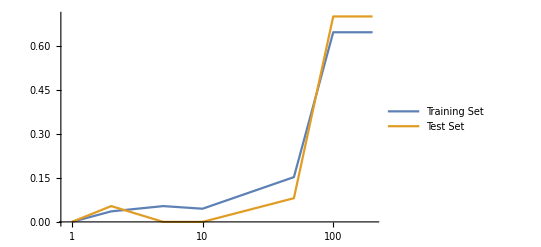

```mathematica
ListLogLinearPlot[{Table[{k[[i]],result[[i,1]]},{i,Length[k]}],
			  Table[{k[[i]],result[[i,2]]},{i,Length[k]}]},Joined->True,PlotLegends->{"Training Set","Test Set"}]
```